```mathematica
(*css zebrafinch model*)
ns := Na ba pa + Nn bn pn;
nh:= Na ba (1-pa) + Nn bn (1-pn);
NNa :=ns vs(lsI vI z +lsO qO + lsV qV) + nh vh(lhI vI z +lhO qO + lhV qV);
NNn :=ns vs(lsI vI (1-z)+lsO(1- qO) + lsV (1-qV)) + nh vh(lhI vI (1-z)+lhO(1- qO) + lhV(1- qV));
qO := (1-u)(Na/(Na +Nn));
qV:= (1-u)(Na ba/(Na ba +Nn bn));
```

```mathematica
AA:=({{0, 0, ba pa, bn pn}, {0, 0, ba(1-pa), bn(1-pn)}, {vs(lsI vI z +lsO qO + lsV qV), vh(lhI vI z +lhO qO + lhV qV), 0, 0}, {vs(lsI vI (1-z)+lsO(1- qO) + lsV (1-qV)), vh(lhI vI (1-z)+lhO(1- qO) + lhV(1- qV)), 0, 0}})
(*exclude vertical learning for simplicities sakes*)
AA=AA/.{lhV -> 0, lsV->0};
```

```mathematica
(*Solve for q-hat when there is no vertical*)
NN = FullSimplify[NNn + NNa]
```

-(ba Na (-1+pa)+bn Nn (-1+pn)) vh (lhO+lhV+lhI vI)+(ba Na pa+bn Nn pn) (lsO+lsV+lsI vI) vs

```mathematica
(* recursion for frequency of adapted adults *)
FFa=FullSimplify[NNa/NN/.{Na->Fa N0,Nn->(1-Fa)N0}]
```

(-(N0 (-ba Fa (-1+pa)+bn (-1+Fa) (-1+pn)) vh (Fa (bn (-1+Fa) lhO-ba (Fa lhO+lhV)) (-1+u)+(bn+ba Fa-bn Fa) lhI vI z))/(bn (-1+Fa)-ba Fa)+N0 (ba Fa pa-bn (-1+Fa) pn) vs (-Fa lsO (-1+u)-(ba Fa lsV (-1+u))/(bn+ba Fa-bn Fa)+lsI vI z))/(-(ba Fa N0 (-1+pa)+bn N0 (-1+Fa+pn-Fa pn)) vh (lhO+lhV+lhI vI)+N0 (ba Fa pa-bn (-1+Fa) pn) (lsO+lsV+lsI vI) vs)

```mathematica
(* verify that FFn + FFa == 1 *)
```

```mathematica
FFn=FullSimplify[NNn/NN/.{Na->Fa N0,Nn->(1-Fa)N0}]
```

(N0 (-(ba Fa (-1+pa)+bn (-1+Fa+pn-Fa pn)) vh (-bn (-1+Fa) (lhO+lhV+Fa lhO (-1+u)+lhI vI-lhI vI z)+ba Fa (lhO+Fa lhO (-1+u)+lhV u+lhI vI-lhI vI z))+(ba Fa pa-bn (-1+Fa) pn) vs (-bn (-1+Fa) (lsO+lsV+Fa lsO (-1+u)+lsI vI-lsI vI z)+ba Fa (lsO+Fa lsO (-1+u)+lsV u+lsI vI-lsI vI z))))/((bn+ba Fa-bn Fa) (-(ba Fa N0 (-1+pa)+bn N0 (-1+Fa+pn-Fa pn)) vh (lhO+lhV+lhI vI)+N0 (ba Fa pa-bn (-1+Fa) pn) (lsO+lsV+lsI vI) vs))

```mathematica
Simplify[FFn+FFa]
```

1

```mathematica
Fasols=Solve[FFa==Fa,Fa]
```

{{Fa→-(-ba^2 lhV vh+3 ba bn lhV vh-2 bn^2 lhV vh+55+bn^2 lhI pn vh vI z-ba^2 lsI pa vI vs z+ba bn lsI pa vI vs z+ba bn lsI pn vI vs z-bn^2 lsI pn vI vs z)/(3 (ba^2 lhV vh-2 ba bn lhV vh+bn^2 lhV vh-ba^2 lhV pa vh+ba bn lhV pa vh+34+bn^2 lsO pn u vs+ba^2 lsI pa vI vs-ba bn lsI pa vI vs-ba bn lsI pn vI vs+bn^2 lsI pn vI vs))-1/1+(1)^(1/3)/(3 2^1 (1))},{Fa→1},{Fa→1}}
 |  |  |  |

```mathematica
Fasols /.{ba->3,bn->1,z->0.6,pa->0.1,pn->0.9,vs->0.8,vh->0.95,vI->0.7  ,lsO-> 0.2 ,lsV-> 0 ,lsI-> 0.8,lhO-> 0.8,lhI-> 0.2 ,lhV-> 0 , lsV -> 0,u-> 0.1 }
Fasols[[1,1,2]]/.{ba->3,bn->1,z->0.6,pa->0.1,pn->0.9,vs->0.8,vh->0.95,vI->0.7  ,lsO-> 0.2 ,lsV-> 0 ,lsI-> 0.8,lhO-> 0.8,lhI-> 0.2  ,lhV-> 0 , lsV -> 0,u-> 0.1 }
Qhat =  Fasols[[1,1,2]]/.{lhV-> 0 , lsV -> 0};
```

{{Fa→0.480835-1.11022×10^-16 ⅈ},{Fa→-1.96121-5.55112×10^-17 ⅈ},{Fa→-0.5+1.11022×10^-16 ⅈ}}

0.480835-1.11022×10^-16 ⅈ

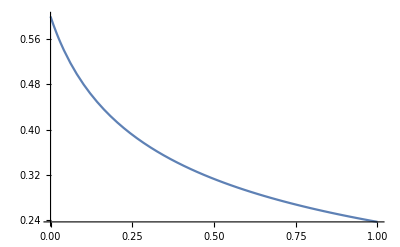

```mathematica
(*plot qhat as a function of u*)
sub={ba->3,bn->1,z->0.6,pa->0.1,pn->0.9,vs->0.8,vh->0.95,vI->0.7  ,lsO-> 0.2 ,lsV-> 0 ,lsI-> 0.8,lhO-> 0.8,lhI-> 0.2  };
Plot[Qhat/.sub,{u,0,1}]
```

```mathematica
Qhat/.{ba->3,bn->1,z->0.8,pa->0,pn->1,vs->0.7,vh->0.9,vI->0.8  ,lsO-> 0.1 ,lsI-> 0.9,lhO-> 0.9,lhI-> 0.1 ,u->0.1}
```

-0.5+4.44089×10^-16 ⅈ

```mathematica
Re[-1.+0. ⅈ]
```

-1.

```mathematica
AA
```

{{0,0,ba pa,bn pn},{0,0,ba (1-pa),bn (1-pn)},{vs ((lsO Na (1-u))/(Na+Nn)+lsI vI z),vh ((lhO Na (1-u))/(Na+Nn)+lhI vI z),0,0},{vs (lsO (1-(Na (1-u))/(Na+Nn))+lsI vI (1-z)),vh (lhO (1-(Na (1-u))/(Na+Nn))+lhI vI (1-z)),0,0}}

```mathematica
(*calc dominamnt eigenvalue*)
LL=Eigenvalues[AA];
LV=Eigenvectors[AA];
```

```mathematica
(*substitute z in for qhat*)
LL1 = Eigenvalues[AA /.{Na->z,Nn->(1-z)}];
LV1 =Eigenvectors[AA/.{Na->z,Nn->(1-z)}];
```

```mathematica
(*4th eigenvalue appears to be dominant*)
LL1/.{ba->2,bn->1,z->0.8,pa->0,pn->1,vs->0.7,vh->0.9,vI->0.8  ,lsO-> 0.1 ,lsI-> 0.9,lhO-> 0.9,lhI-> 0.1 ,u->0.1}
```

{0.-0.211177 ⅈ,0.+0.211177 ⅈ,-1.20275,1.20275}

```mathematica
(*calculate eigenvectors*)
LV1/.{ba->2,bn->1,z->0.8,pa->0,pn->1,vs->0.7,vh->0.9,vI->0.8  ,lsO-> 0.1 ,lsI-> 0.9,lhO-> 0.9,lhI-> 0.1 ,u->0.1}
```

{{0.+4.73536 ⅈ,0.-3.23928 ⅈ,-0.342031,1},{0.-4.73536 ⅈ,0.+3.23928 ⅈ,-0.342031,1},{-0.831431,-4.57148,2.74916,1},{0.831431,4.57148,2.74916,1}}

```mathematica
LL1[[4]]
```

√((bn lhO vh)/2-1/2 bn lhO pn vh+1/2 bn lhI vh vI-1/2 bn lhI pn vh vI+1/2 bn lsO pn vs+1/2 bn lsI pn vI vs+1/2 ba lhO vh z-1/2 bn lhO vh z-1/2 ba lhO pa vh z+1/2 bn lhO pn vh z-1/2 ba lhO u vh z+1/2 bn lhO u vh z+1/2 ba lhO pa u vh z-1/2 bn lhO pn u vh z+1/2 ba lhI vh vI z-1/2 bn lhI vh vI z-1/2 ba lhI pa vh vI z+1/2 bn lhI pn vh vI z+1/2 ba lsO pa vs z-1/2 bn lsO pn vs z-1/2 ba lsO pa u vs z+1/2 bn lsO pn u vs z+1/2 ba lsI pa vI vs z-1/2 bn lsI pn vI vs z+1/2 √((-bn lhO vh+bn lhO pn vh-bn lhI vh vI+bn lhI pn vh vI-bn lsO pn vs-bn lsI pn vI vs-ba lhO vh z+bn lhO vh z+ba lhO pa vh z-bn lhO pn vh z+ba lhO u vh z-bn lhO u vh z-ba lhO pa u vh z+bn lhO pn u vh z-ba lhI vh vI z+bn lhI vh vI z+ba lhI pa vh vI z-bn lhI pn vh vI z-ba lsO pa vs z+bn lsO pn vs z+ba lsO pa u vs z-bn lsO pn u vs z-ba lsI pa vI vs z+bn lsI pn vI vs z)^2-4 (ba bn lhO lsI pa u vh vI vs z-ba bn lhI lsO pa u vh vI vs z-ba bn lhO lsI pn u vh vI vs z+ba bn lhI lsO pn u vh vI vs z)))

```mathematica
Lambda1[lsI_, lhI_, lsO_, lhO_]:=√((bn lhO vh)/2-1/2 bn lhO pn vh+1/2 bn lhI vh vI-1/2 bn lhI pn vh vI+1/2 bn lsO pn vs+1/2 bn [lsI ]pn vI vs+1/2 ba lhO vh z-1/2 bn lhO vh z-1/2 ba lhO pa vh z+1/2 bn lhO pn vh z-1/2 ba lhO u vh z+1/2 bn lhO u vh z+1/2 ba lhO pa u vh z-1/2 bn lhO pn u vh z+1/2 ba lhI vh vI z-1/2 bn lhI vh vI z-1/2 ba lhI pa vh vI z+1/2 bn lhI pn vh vI z+1/2 ba lsO pa vs z-1/2 bn lsO pn vs z-1/2 ba lsO pa u vs z+1/2 bn lsO pn u vs z+1/2 ba [lsI] pa vI vs z-1/2 bn [lsI] pn vI vs z+1/2 √((-bn lhO vh+bn lhO pn vh-bn lhI vh vI+bn lhI pn vh vI-bn lsO pn vs-bn [lsI ]pn vI vs-ba lhO vh z+bn lhO vh z+ba lhO pa vh z-bn lhO pn vh z+ba lhO u vh z-bn lhO u vh z-ba lhO pa u vh z+bn lhO pn u vh z-ba lhI vh vI z+bn lhI vh vI z+ba lhI pa vh vI z-bn lhI pn vh vI z-ba lsO pa vs z+bn lsO pn vs z+ba lsO pa u vs z-bn lsO pn u vs z-ba [lsI] pa vI vs z+bn [lsI ]pn vI vs z)^2-4 (ba bn lhO [lsI] pa u vh vI vs z-ba bn lhI lsO pa u vh vI vs z-ba bn lhO [lsI] pn u vh vI vs z+ba bn lhI lsO pn u vh vI vs z)));
```

```mathematica
DlsI:=D[Lambda1[lsI, lhI, lsO, lhO],lsI];
```

```mathematica
DlhI:=D[Lambda1[lsI, lhI, lsO, lhO],lhI];
```

```mathematica
DlsO:=D[Lambda1[lsI, lhI, lsO, lhO],lsO];
```

```mathematica
DlhO:=D[Lambda1[lsI, lhI, lsO, lhO],lhO];
```

```mathematica
(*try and graph*)
lsIstart=0.25;
imax=20;
Ptab=Table[0,{i,imax}];
delta=0.05;
sub={ba->2,bn->1,z->0.5,pa->0,pn->1,vs->0.7,vh->0.9,vI->0.8  ,lsO-> (lsIstart-delta) ,lhO-> 0.5,lhI-> 0.5 ,u->0.01};
lsItab[[1]]=lsIstart;
```

```mathematica
For[i=2,i<imax,i++,{
Ptab[[i]]=Ptab[[i-1]]+delta DlsI/.sub/.{P->Ptab[[i-1]]};
Ptab[[i]]=If[Ptab[[i]]>1,1,Ptab[[i]]];
Ptab[[i]]=If[Ptab[[i]]<0,0,Ptab[[i]]];
}];
Ptab
```

{0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0}

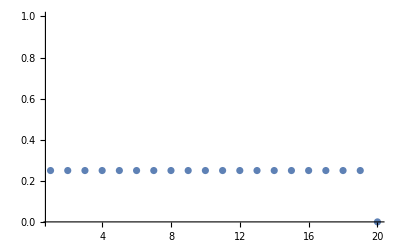

```mathematica
ListPlot[Ptab,PlotRange->{All,{0,1}}]
```

```mathematica
(*Partial derivative example*)
f[x_,y_]:=Sin[x]+x^2 + 3y^2
```

```mathematica
D[f[x,y],x]
```

2 x+Cos[x]

```mathematica
D[f[x,y],y]
```

6 y